## Calculating the mobius Function of a partition lattice

```mathematica
SubSetQ[large_,small_]:=Sort[Intersection[large,small]]==Sort[small]
```

```mathematica
SubSetQ[{1,2,3},{2,3}]
```

True

```mathematica
Mobius[partition1_,partition2_]:=Block[{
c1=Length[partition1],
c2=Length[partition2], 
sorted1=Sort[Map[Sort,partition1]], 
sorted2=Sort[Map[Sort,partition2]],
counts,
counts2,
position,
found,
foundFactor=1
},
If[c1==c2,
If[sorted1==sorted2,1,0]
,
If[c1>c2,
counts=Table[0,c2];
Table[
position=1;
found=False;
Table[
If[SubsetQ[largeSet, smallSet],
counts[[position]]=counts[[position]]+1;
found=True
,{largeSet,sorted2}
];
position++;,
{largeSet,sorted2}
];
If[!found,foundFactor=0]
,{smallSet, sorted1}
];
counts2=Map[If[#==0,0,(#-1)!]&,counts];
foundFactor*Apply[Times,counts2]*(-1)^(c1-c2)
,
0
]
]
]
```

```mathematica
Mobius[{{1},{2},{3},{6}},{{1,2,3},{6}}]
```

2

```mathematica
Mobius[{{1,2},{3},{6}},{{1,2,3},{6}}]
```

-1

```mathematica
Mobius[{{1,2,3},{6}},{{1,2,3},{6}}]
```

1

```mathematica
Mobius[{{1,2,3,6}},{{1,2,3},{6}}]
```

0

## Now prepare sorted partitions

```mathematica
allGraphs6AtomKeysSorted=Sort[allGraphs6AtomKeys,CompareSymbols[allGraphs6[#1,"colofour"],allGraphs6[#2,"colofour"]]&];
```

```mathematica
Length[allGraphs6AtomKeysSorted]
```

203

```mathematica
allGraphs6NullAtomKeysSorted=Sort[allGraphs6NullAtomKeys,CompareSymbols[allGraphs6[#1,"colofourrealnull"],allGraphs6[#2,"colofourrealnull"]]&];
```

```mathematica
Vector6[key_]:=Table[Coefficient[allGraphs6[key,"colofourrealnull"],allGraphs6[k,"colofourrealnull"]],{k, allGraphs6NullAtomKeysSorted}]
```

```mathematica
Vector6Full[key_]:=Table[Coefficient[allGraphs6[key,"colofour"],allGraphs6[k,"colofour"]],{k, allGraphs6AtomKeysSorted}]
```

```mathematica
mobMat=Table[
Mobius[allGraphs6[i,"vertexsets"],allGraphs6[j,"vertexsets"]]
,{i,allGraphs6NullAtomKeysSorted},{j,allGraphs6NullAtomKeysSorted}
];
```

```mathematica
SymbolToLabel[s_]:=Row[Riffle[ StringSplit[StringDrop[SymbolName[s ],1],"x"],Style["|",Bold,Red]]]
```

```mathematica
MatrixForm[mobMat
,
TableHeadings->{Table[SymbolToLabel[allGraphs6[k,"colofourrealnull"]],{k,allGraphs6NullAtomKeysSorted}], Table[Rotate[SymbolToLabel[allGraphs6[k,"colofourrealnull"]],Pi/2],{k,allGraphs6NullAtomKeysSorted}]}
]
```

(1)
 |  |  |  |

```mathematica
Tr[mobMat]
```

203

```mathematica
allGraphs6[0,"graph"]
```

-Graphics-

-Graphics-

```mathematica
Vector6Full[0]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
Vector6[0]
```

{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Table[Vector6Full[k].mobMat==Vector6[k],{k,Keys[allGraphs6]}]
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,52945,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}
 |  |  |  |

```mathematica
MatrixForm[Inverse[mobMat]
,
TableHeadings->{Table[SymbolToLabel[allGraphs6[k,"colofourrealnull"]],{k,allGraphs6NullAtomKeysSorted}], Table[Rotate[SymbolToLabel[allGraphs6[k,"colofourrealnull"]],Pi/2],{k,allGraphs6NullAtomKeysSorted}]}
]
```

(1)
 |  |  |  |

```mathematica
Vector6Full[271]
```

{1,0,1,1,0,1,0,1,1,1,1,1,1,1,1,1,0,1,0,0,1,1,0,1,0,1,0,0,1,0,1,0,1,1,0,1,0,0,1,1,1,1,1,0,1,0,1,1,1,1,0,0,1,1,1,1,0,1,1,1,1,0,0,0,0,0,1,0,1,1,0,1,1,1,1,0,1,0,1,1,0,0,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,1,1,0,1,0,1,0,0,1,0,1,0,1,1,0,0,0,0,1,1,1,0,0,0,0,1,0,0,0,1,1,1,1,1,0,0,0,1,0,0,0,0,0,1,1,0,0,0,0,0,0,1,0,1,1,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Vector6[271]
```

{1,-1,0,0,-1,0,-1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Table[Indexed[x,i],{i,1,15}]
```

{x1,x2,x3,x4,x5,x6,x7,x8,x9,x10,x11,x12,x13,x14,x15}

```mathematica
{x1,x2,x3,x6,x5,x6,x7,x8,x9,x10,x11,x12,x13,x16,x15}
```

```mathematica
Table[Indexed[x,i],{i,1,15}].mobMat
```

Dot::dotsh: Tensors {x,x,x,x,x,x,x,x,x,x,x,x,x,x,x} and … have incompatible shapes.

{x1,x2,x3,x4,x5,x6,x7,x8,x9,x10,x11,x12,x13,x14,x15}.{{1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,4,4,4,4,4,4,4,4,4,4,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,24,24,24,24,24,24,-120},201,{0,0,0,0,0,0,0,0,0,0,183,0,0,0,0,0,0,0,0,0,1}}
 |  |  |  |

```mathematica
{x1,-x1+x2,-x1+x3,-x1+x6,-x1+x5,-x1+x6,-x1+x7,2 x1-x2-x3-x6+x8,x1-x2-x5+x9,2 x1-x3-x5-x6+x10,2 x1-x6-x5-x7+x11,x1-x6-x6+x12,2 x1-x2-x6-x7+x13,x1-x3-x7+x16,-6 x1+2 x2+2 x3+2 x6+2 x5+2 x6+2 x7-x8-x9-x10-x11-x12-x13-x16+x15}
```

```mathematica
Solve[x1==0&&-x1+x2==0&&-x1+x3==0&&-x1+x6==0  ]
```

{{x1→0,x2→0,x3→0,x6→0}}

```mathematica
{{x1->0,x2->0,x3->0,x6->0}}
```

```mathematica
Table[Indexed[x,i],{i,1,15}].Inverse[mobMat]
```

Dot::dotsh: Tensors {x,x,x,x,x,x,x,x,x,x,x,x,x,x,x} and {{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,«153»},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,«153»},{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,«153»},«45»,{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,«153»},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,«153»},«153»} have incompatible shapes.

{x1,x2,x3,x4,x5,x6,x7,x8,x9,x10,x11,x12,x13,x14,x15}.{1}
 |  |  |  |

```mathematica
{x1,x1+x2,x1+x3,x1+x6,x1+x5,x1+x6,x1+x7,x1+x2+x3+x6+x8,x1+x2+x5+x9,x1+x3+x5+x6+x10,x1+x6+x5+x7+x11,x1+x6+x6+x12,x1+x2+x6+x7+x13,x1+x3+x7+x16,x1+x2+x3+x6+x5+x6+x7+x8+x9+x10+x11+x12+x13+x16+x15}
```

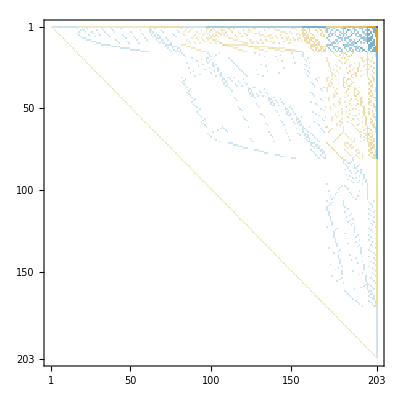

```mathematica
MatrixPlot[mobMat]
```

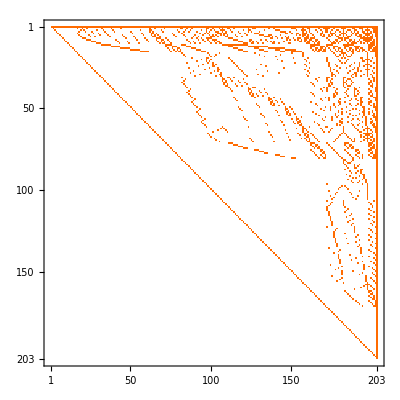

```mathematica
MatrixPlot[Inverse[mobMat]]
```

```mathematica
colors=Table[Table[If[OddQ[k],LightBlue,LightYellow],{i,StirlingS2[6,7-k]}],{k,1,6}]//Flatten
```

{RGBColor[0.87, 0.94, 1],RGBColor[1, 1, 0.85],RGBColor[1, 1, 0.85],RGBColor[1, 1, 0.85],RGBColor[1, 1, 0.85],RGBColor[1, 1, 0.85],RGBColor[1, 1, 0.85],RGBColor[1, 1, 0.85],RGBColor[1, 1, 0.85],RGBColor[1, 1, 0.85],RGBColor[1, 1, 0.85],RGBColor[1, 1, 0.85],RGBColor[1, 1, 0.85],RGBColor[1, 1, 0.85],RGBColor[1, 1, 0.85],RGBColor[1, 1, 0.85],RGBColor[0.87, 0.94, 1],RGBColor[0.87, 0.94, 1],RGBColor[0.87, 0.94, 1],RGBColor[0.87, 0.94, 1],RGBColor[0.87, 0.94, 1],RGBColor[0.87, 0.94, 1],RGBColor[0.87, 0.94, 1],RGBColor[0.87, 0.94, 1],RGBColor[0.87, 0.94, 1],RGBColor[0.87, 0.94, 1],RGBColor[0.87, 0.94, 1],RGBColor[0.87, 0.94, 1],RGBColor[0.87, 0.94, 1],RGBColor[0.87, 0.94, 1],RGBColor[0.87, 0.94, 1],RGBColor[0.87, 0.94, 1],RGBColor[0.87, 0.94, 1],RGBColor[0.87, 0.94, 1],RGBColor[0.87, 0.94, 1],RGBColor[0.87, 0.94, 1],RGBColor[0.87, 0.94, 1],RGBColor[0.87, 0.94, 1],RGBColor[0.87, 0.94, 1],RGBColor[0.87, 0.94, 1],RGBColor[0.87, 0.94, 1],RGBColor[0.87, 0.94, 1],RGBColor[0.87, 0.94, 1],RGBColor[0.87, 0.94, 1],RGBColor[0.87, 0.94, 1],RGBColor[0.87, 0.94, 1],RGBColor[0.87, 0.94, 1],RGBColor[0.87, 0.94, 1],RGBColor[0.87, 0.94, 1],RGBColor[0.87, 0.94, 1],RGBColor[0.87, 0.94, 1],RGBColor[0.87, 0.94, 1],RGBColor[0.87, 0.94, 1],RGBColor[0.87, 0.94, 1],RGBColor[0.87, 0.94, 1],RGBColor[0.87, 0.94, 1],RGBColor[0.87, 0.94, 1],RGBColor[0.87, 0.94, 1],RGBColor[0.87, 0.94, 1],RGBColor[0.87, 0.94, 1],RGBColor[0.87, 0.94, 1],RGBColor[0.87, 0.94, 1],RGBColor[0.87, 0.94, 1],RGBColor[0.87, 0.94, 1],RGBColor[0.87, 0.94, 1],RGBColor[0.87, 0.94, 1],RGBColor[0.87, 0.94, 1],RGBColor[0.87, 0.94, 1],RGBColor[0.87, 0.94, 1],RGBColor[0.87, 0.94, 1],RGBColor[0.87, 0.94, 1],RGBColor[0.87, 0.94, 1],RGBColor[0.87, 0.94, 1],RGBColor[0.87, 0.94, 1],RGBColor[0.87, 0.94, 1],RGBColor[0.87, 0.94, 1],RGBColor[0.87, 0.94, 1],RGBColor[0.87, 0.94, 1],RGBColor[0.87, 0.94, 1],RGBColor[0.87, 0.94, 1],RGBColor[0.87, 0.94, 1],RGBColor[1, 1, 0.85],RGBColor[1, 1, 0.85],RGBColor[1, 1, 0.85],RGBColor[1, 1, 0.85],RGBColor[1, 1, 0.85],RGBColor[1, 1, 0.85],RGBColor[1, 1, 0.85],RGBColor[1, 1, 0.85],RGBColor[1, 1, 0.85],RGBColor[1, 1, 0.85],RGBColor[1, 1, 0.85],RGBColor[1, 1, 0.85],RGBColor[1, 1, 0.85],RGBColor[1, 1, 0.85],RGBColor[1, 1, 0.85],RGBColor[1, 1, 0.85],RGBColor[1, 1, 0.85],RGBColor[1, 1, 0.85],RGBColor[1, 1, 0.85],RGBColor[1, 1, 0.85],RGBColor[1, 1, 0.85],RGBColor[1, 1, 0.85],RGBColor[1, 1, 0.85],RGBColor[1, 1, 0.85],RGBColor[1, 1, 0.85],RGBColor[1, 1, 0.85],RGBColor[1, 1, 0.85],RGBColor[1, 1, 0.85],RGBColor[1, 1, 0.85],RGBColor[1, 1, 0.85],RGBColor[1, 1, 0.85],RGBColor[1, 1, 0.85],RGBColor[1, 1, 0.85],RGBColor[1, 1, 0.85],RGBColor[1, 1, 0.85],RGBColor[1, 1, 0.85],RGBColor[1, 1, 0.85],RGBColor[1, 1, 0.85],RGBColor[1, 1, 0.85],RGBColor[1, 1, 0.85],RGBColor[1, 1, 0.85],RGBColor[1, 1, 0.85],RGBColor[1, 1, 0.85],RGBColor[1, 1, 0.85],RGBColor[1, 1, 0.85],RGBColor[1, 1, 0.85],RGBColor[1, 1, 0.85],RGBColor[1, 1, 0.85],RGBColor[1, 1, 0.85],RGBColor[1, 1, 0.85],RGBColor[1, 1, 0.85],RGBColor[1, 1, 0.85],RGBColor[1, 1, 0.85],RGBColor[1, 1, 0.85],RGBColor[1, 1, 0.85],RGBColor[1, 1, 0.85],RGBColor[1, 1, 0.85],RGBColor[1, 1, 0.85],RGBColor[1, 1, 0.85],RGBColor[1, 1, 0.85],RGBColor[1, 1, 0.85],RGBColor[1, 1, 0.85],RGBColor[1, 1, 0.85],RGBColor[1, 1, 0.85],RGBColor[1, 1, 0.85],RGBColor[1, 1, 0.85],RGBColor[1, 1, 0.85],RGBColor[1, 1, 0.85],RGBColor[1, 1, 0.85],RGBColor[1, 1, 0.85],RGBColor[1, 1, 0.85],RGBColor[1, 1, 0.85],RGBColor[1, 1, 0.85],RGBColor[1, 1, 0.85],RGBColor[1, 1, 0.85],RGBColor[1, 1, 0.85],RGBColor[1, 1, 0.85],RGBColor[1, 1, 0.85],RGBColor[1, 1, 0.85],RGBColor[1, 1, 0.85],RGBColor[1, 1, 0.85],RGBColor[1, 1, 0.85],RGBColor[1, 1, 0.85],RGBColor[1, 1, 0.85],RGBColor[1, 1, 0.85],RGBColor[1, 1, 0.85],RGBColor[1, 1, 0.85],RGBColor[1, 1, 0.85],RGBColor[1, 1, 0.85],RGBColor[1, 1, 0.85],RGBColor[0.87, 0.94, 1],RGBColor[0.87, 0.94, 1],RGBColor[0.87, 0.94, 1],RGBColor[0.87, 0.94, 1],RGBColor[0.87, 0.94, 1],RGBColor[0.87, 0.94, 1],RGBColor[0.87, 0.94, 1],RGBColor[0.87, 0.94, 1],RGBColor[0.87, 0.94, 1],RGBColor[0.87, 0.94, 1],RGBColor[0.87, 0.94, 1],RGBColor[0.87, 0.94, 1],RGBColor[0.87, 0.94, 1],RGBColor[0.87, 0.94, 1],RGBColor[0.87, 0.94, 1],RGBColor[0.87, 0.94, 1],RGBColor[0.87, 0.94, 1],RGBColor[0.87, 0.94, 1],RGBColor[0.87, 0.94, 1],RGBColor[0.87, 0.94, 1],RGBColor[0.87, 0.94, 1],RGBColor[0.87, 0.94, 1],RGBColor[0.87, 0.94, 1],RGBColor[0.87, 0.94, 1],RGBColor[0.87, 0.94, 1],RGBColor[0.87, 0.94, 1],RGBColor[0.87, 0.94, 1],RGBColor[0.87, 0.94, 1],RGBColor[0.87, 0.94, 1],RGBColor[0.87, 0.94, 1],RGBColor[0.87, 0.94, 1],RGBColor[1, 1, 0.85]}

```mathematica
colors2=Table[Table[If[OddQ[k],Blue,Yellow],{i,StirlingS2[6,7-k]}],{k,1,6}]//Flatten
```

{RGBColor[0, 0, 1],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[1, 1, 0]}

```mathematica
mobMat
```

{{1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,4,4,4,4,4,4,4,4,4,4,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,24,24,24,24,24,24,-120},202}
 |  |  |  |

```mathematica
allGraphs6AtomKeysSorted
```

{7174453,7174454,7174462,7174456,7174696,7174534,7174480,7194136,7181014,7176640,7175182,11957422,8768776,7705894,7351600,7233502,7174697,7174537,7174489,7194137,7194145,7194139,7181015,7181095,7181041,7176643,7176883,7176667,7175191,7175425,7175263,11957423,11957431,11957425,11957665,11957503,11957449,8768777,8768785,8768779,8775337,8770963,8769505,7705895,7705975,7705921,7725577,7708081,7706623,7351603,7351843,7351627,7371283,7358161,7352329,7233511,7233745,7233583,7253185,7240063,7235689,7174466,7174786,7174726,7174562,7200940,7196404,7194892,7183210,7181746,7177370,13571428,12495424,12136756,12017200,9300460,8946004,8827852,7883050,7764946,7410650,11957666,11957506,11957458,8775338,8770966,8769514,7725578,7708108,7706704,7371286,7358188,7352572,7253194,7240144,7235932,7194149,7200941,7196407,7194901,7181123,7183237,7181827,7176913,7177613,7175515,11957435,11957755,11957695,11957531,13571429,13571437,13571431,12495425,12495505,12495451,12136759,12136999,12136783,12017209,12017443,12017281,8768789,8777533,8776069,8771693,9300461,9302647,9301189,8946007,8952565,8946733,8827861,8834413,8830039,7706003,7727845,7726333,7708811,7883077,7902733,7883779,7765027,7784629,7767133,7351873,7378087,7372039,7358893,7410893,7430333,7417211,7233835,7259989,7255453,7242259,7174817,7203217,7201699,7197161,7183943,14109673,13750843,13631233,12674767,12555205,12196535,9477697,9359539,9005081,7942103,13571441,12495533,12137029,12017533,9303377,8953297,8836609,7903489,7786897,7437137,11957786,14109674,13750846,13631242,12674794,12555286,12196778,8778266,9478426,9361726,9011642,7728602,7961786,7378846,7262266,7203977,14289097,14169481,13810649,12734549,9536777,14348906}

```mathematica
Table[SymbolToLabel[allGraphs6[k,"colofour"]],{k,allGraphs6AtomKeysSorted}]
```

{1|2|3|4|5|6,1|2|3|4|56,1|2|3|45|6,1|2|3|46|5,1|2|34|5|6,1|2|35|4|6,1|2|36|4|5,1|23|4|5|6,1|24|3|5|6,1|25|3|4|6,1|26|3|4|5,12|3|4|5|6,13|2|4|5|6,14|2|3|5|6,15|2|3|4|6,16|2|3|4|5,1|2|34|56,1|2|35|46,1|2|36|45,1|23|4|56,1|23|45|6,1|23|46|5,1|24|3|56,1|24|35|6,1|24|36|5,1|25|3|46,1|25|34|6,1|25|36|4,1|26|3|45,1|26|34|5,1|26|35|4,12|3|4|56,12|3|45|6,12|3|46|5,12|34|5|6,12|35|4|6,12|36|4|5,13|2|4|56,13|2|45|6,13|2|46|5,13|24|5|6,13|25|4|6,13|26|4|5,14|2|3|56,14|2|35|6,14|2|36|5,14|23|5|6,14|25|3|6,14|26|3|5,15|2|3|46,15|2|34|6,15|2|36|4,15|23|4|6,15|24|3|6,15|26|3|4,16|2|3|45,16|2|34|5,16|2|35|4,16|23|4|5,16|24|3|5,16|25|3|4,1|2|3|456,1|2|345|6,1|2|346|5,1|2|356|4,1|234|5|6,1|235|4|6,1|236|4|5,1|245|3|6,1|246|3|5,1|256|3|4,123|4|5|6,124|3|5|6,125|3|4|6,126|3|4|5,134|2|5|6,135|2|4|6,136|2|4|5,145|2|3|6,146|2|3|5,156|2|3|4,12|34|56,12|35|46,12|36|45,13|24|56,13|25|46,13|26|45,14|23|56,14|25|36,14|26|35,15|23|46,15|24|36,15|26|34,16|23|45,16|24|35,16|25|34,1|23|456,1|234|56,1|235|46,1|236|45,1|24|356,1|245|36,1|246|35,1|25|346,1|256|34,1|26|345,12|3|456,12|345|6,12|346|5,12|356|4,123|4|56,123|45|6,123|46|5,124|3|56,124|35|6,124|36|5,125|3|46,125|34|6,125|36|4,126|3|45,126|34|5,126|35|4,13|2|456,13|245|6,13|246|5,13|256|4,134|2|56,134|25|6,134|26|5,135|2|46,135|24|6,135|26|4,136|2|45,136|24|5,136|25|4,14|2|356,14|235|6,14|236|5,14|256|3,145|2|36,145|23|6,145|26|3,146|2|35,146|23|5,146|25|3,15|2|346,15|234|6,15|236|4,15|246|3,156|2|34,156|23|4,156|24|3,16|2|345,16|234|5,16|235|4,16|245|3,1|2|3456,1|2345|6,1|2346|5,1|2356|4,1|2456|3,1234|5|6,1235|4|6,1236|4|5,1245|3|6,1246|3|5,1256|3|4,1345|2|6,1346|2|5,1356|2|4,1456|2|3,123|456,124|356,125|346,126|345,134|256,135|246,136|245,145|236,146|235,156|234,12|3456,1234|56,1235|46,1236|45,1245|36,1246|35,1256|34,13|2456,1345|26,1346|25,1356|24,14|2356,1456|23,15|2346,16|2345,1|23456,12345|6,12346|5,12356|4,12456|3,13456|2,123456}

```mathematica
coloured6=TableForm[Table[Framed[If[mobMat[[i,j]]==0,"",mobMat[[i,j]]],Background->If[mobMat[[i,j]]==0,colors[[j]],Red],ContentPadding->False,ImageSize->{30,30}, FrameStyle->Directive[colors2[[i]]]],{i,1,203},{j,1,203}],TableSpacing->{0, 0},TableHeadings->{Table[SymbolToLabel[allGraphs6[k,"colofour"]],{k,allGraphs6AtomKeysSorted}], Table[Rotate[SymbolToLabel[allGraphs6[k,"colofour"]],Pi/2],{k,allGraphs6AtomKeysSorted}]}]
```

1
 |  |  |  |

```mathematica
Export["D:\\Saved\\Exports\\6\\BandedMobius.png",coloured6,ImageResolution->200]
```

D:\Saved\Exports\6\BandedMobius.png